Last modified on: Wednesday, July 11, 2018 at 6:34

Author Info

Sabrina Kuhrn

Tuseeta Banerjee

Unicredit Bank Austria

Poster Session Content

Automatic Data Visualization

Design heuristic rules to automatically visualize various types of data. The project would combine statistical analysis, unsupervised/clustering methods along with the wide variety of visualization techniques Wolfram Language has to offer.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

‘A picture is worth a thousand words’ - While trying to obtain information from large volumes of data, it is useful to visualize it in a meaningful way. However, the greatest challenge is to find the appropriate tool to visualize the underlying data. In this project, we have explored the various kinds of data visualization tools the Wolfram Language offers, and have come up with automatic rules to infer the data type and decide automatically the exact plot type to use for the data.  As the Wolfram Data Repository offers a large amount of curated data, we used examples from there.

As large volumes of data imply a high number of visualization methods, there are way more informative visualization techniques that can be explored further.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Different data types

Before looking at structures,  features, pattern, trends, relationships etc. in data, different data types are extracted, to apply the appropriate visualization tools. We focused on the following types:

Nominal and Text (“IBRD Statement of Loans”)

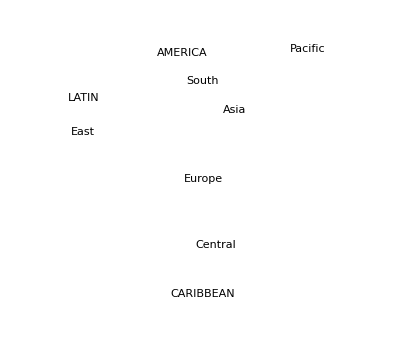
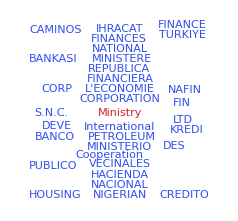
conditionalPlot[posT,"Nominal",nomP];
conditionalPlot[posT,"Text",nomP];
-Graphics-  -Graphics--Graphics--Graphics-

Image (“MNIST”)

imagePlot[posT,intI];
-Graphics-

Numerical plots (“Mass Shootings in America”)

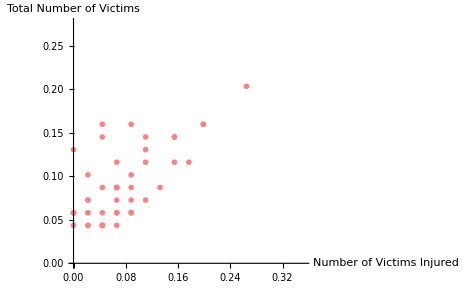
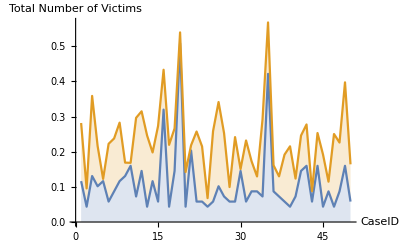
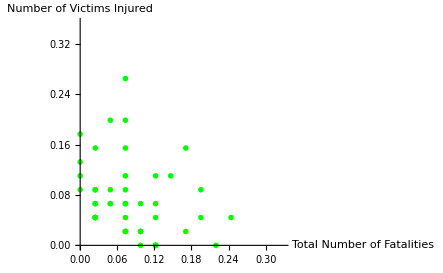
numericPlot[posT,"Numerical","H",intN]
-Graphics--Graphics--Graphics-

Time Series (““IBRD Statement of Loans””)

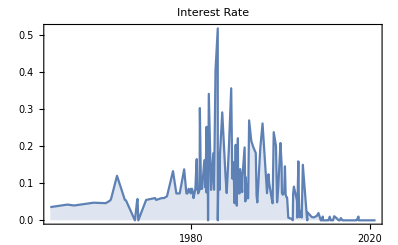
timeSeriesPlot[posT,intT];
-Graphics-

GeoHistogram (“Mass Shootings in America”)

geoPlot[posT];
-Graphics-

Running the whole Function:

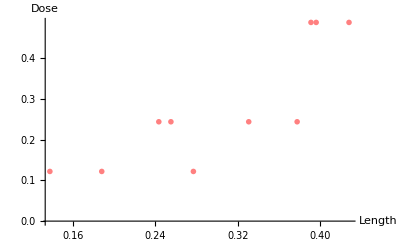
MainFunction[ResourceObject["Sample Data: Guinea Pig Tooth Growth"]]
-Graphics--Graphics-

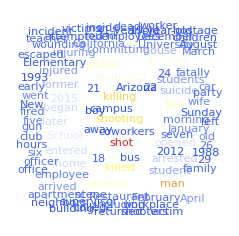
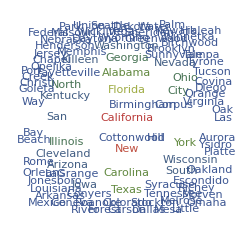
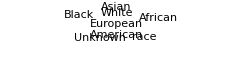
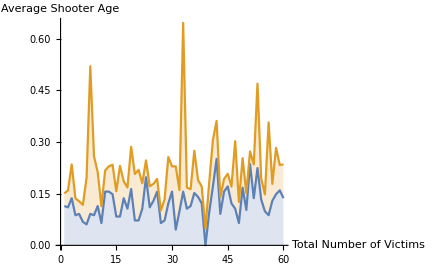
MainFunction[ResourceObject["Mass Shootings in America"],60]
-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

https://github.com/Eunike91/Summer2018Starter/blob/master/StudentDeliverables/DataVisualization.nb

#### Links

https://datarepository.wolframcloud.com/

#### Keywords

automated visualization

data analysis

wolfram data repository